```mathematica
a=Import["G:\\calc-online\\gpd\\k-result\\diagram-m-t.wdx"];
f1=Query[1,1]@a;
g1=Query[1,2]@a;
f2=Query[2,1]@a;
g2=Query[2,2]@a;
```

```mathematica
(*q3=(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)*)
f12=f1/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
f22=f2/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g12=g1/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g22=g2/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
```

```mathematica
nf1[ξ_]=(I*y*f12)/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,Q->1,Λ->1};
ng1[ξ_]=(I*y*g12)/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,Q->1,Λ->1};
nf2[ξ_]=(I*y*f22)/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,Q->1,Λ->1};
ng2[ξ_]=(I*y*g22)/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,Q->1,Λ->1};
```

```mathematica
inf[ξ_]:=NIntegrate[Simplify[nf1[ξ]],{y,-ξ,ξ},{k3,0,∞},{θ,0,2π},WorkingPrecision->10]+NIntegrate[Simplify[nf2[ξ]],{y,ξ,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10];

ing[ξ_]:=NIntegrate[Simplify[ng1[ξ]],{y,-ξ,ξ},{k3,0,∞},{θ,0,2π},WorkingPrecision->10]+NIntegrate[Simplify[ng2[ξ]],{y,ξ,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10];
```

```mathematica
ing[0.001]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in k3 near {y,k3,θ} = {-0.000577938199597078687600348366484458759884559445567793416295841,1.64168103373044941445919192179383377392577510987682303036287×10^690538901,2.65189250301339853731380469386283314886491875718014675960719}. NIntegrate obtained 0.0000270253764765242375995390397129390948136056159871741433640109 and 0.000013342300164747267972576514270205974508325671238950374980816 for the integral and error estimates.

-0.241451137

```mathematica
ing[0.01]
```

-0.241512018

```mathematica
inf[0.01]
```

0.0567539682

```mathematica
inf[0.001]
```

0.0567152584

```mathematica
lf=Parallelize[Table[{ξ,inf[ξ]},{ξ,0,0.4,0.01}]];
lg=Parallelize[Table[{ξ,ing[ξ]},{ξ,0,0.4,0.01}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

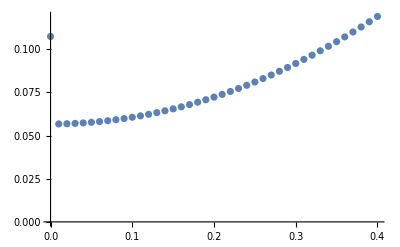

```mathematica
ListPlot[lf]
```

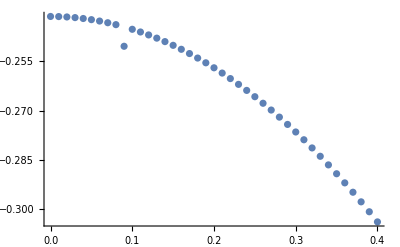

```mathematica
ListPlot[lg]
```

```mathematica
FindFit[%27,a*x^2+b,{a,b},x]
```

FindFit::ivar: <|1→<|f→(k3 (4 MB^2 P1 ξ^2 (-(2 ⅈ P1 π («1»)^2 («1673»+2 MB P1^4 («1»)^4 («1») («4»+«1»)^2))/(3 MB «1» «1» (-2 k3^2 P1 ξ-2 mm^2 P1 ξ+«1»+«1»-(«1»)/(2 ξ)-«1») («1»)^2)+(«1»)/(«1»))-«1»))/(8 P1^2 (4 MB^2 ξ^2+Q^2 (-1+ξ^2))),g→(k3 (MB^2 P1 («1») (-(2 ⅈ «2» («1»)^2 («1»))/(3 «4» («1»)^2)+(«1»)/(«1»))-«1»))/(2 P1^2 (4 MB^2 ξ^2+Q^2 (-1+ξ^2)))|>,2→<|f→(k3 (-«1»+«1»))/(8 «1» («1»+«1»)),g→«1»|>|> is not a valid variable.

FindFit[{{0.,0.107423162},{0.01,0.0567539682},37,{0.39,0.115940359},{0.4,0.119019981}},<|1→<|1|>,2→1|>,{1},x]
 |  |  |  |

```mathematica
lf
```

{{0.,0.107423162},{0.01,0.0567539682},{0.02,0.0568707901},{0.03,0.0570651018},{0.04,0.057338161},{0.05,0.0576899873},{0.06,0.0581170848},{0.07,0.0586233141},{0.08,0.0592068149},{0.09,0.0598691061},{0.1,0.0606093862},{0.11,0.0614267252},{0.12,0.0623220617},{0.13,0.0632954662},{0.14,0.0643470581},{0.15,0.0654759872},{0.16,0.0666818633},{0.17,0.0679636191},{0.18,0.0693320685},{0.19,0.0707712269},{0.2,0.0722907484},{0.21,0.0738856934},{0.22,0.0755622076},{0.23,0.0773116226},{0.24,0.0791426101},{0.25,0.0810521899},{0.26,0.083036984},{0.27,0.085101782},{0.28,0.0872429913},{0.29,0.089462072},{0.3,0.0917603216},{0.31,0.0941369265},{0.32,0.0965896694},{0.33,0.0991205276},{0.34,0.101729813},{0.35,0.104417658},{0.36,0.107182623},{0.37,0.110023716},{0.38,0.112944859},{0.39,0.115940359},{0.4,0.119019981}}

```mathematica
l1={{0.01,0.05675396816927138039522595649210222398`9.554855570661106},{0.02,0.05687079013206583270531812699093092846`9.555334756598352},{0.03,0.05706510177835368271049705066514095316`9.556053245979033},{0.04,0.05733816097335345926902463374166905081`9.556980102031787},{0.05,0.05768998729591673926399696317619412791`9.558084129344945},{0.06,0.05811708481991892714071918628972219381`9.559309671219781},{0.06999999999999999,0.05862331405349277915538784765563946221`9.560678109388075},{0.08,0.05920681488346402213190659772818249038`9.562171150680387},{0.09,0.05986910607389311419653483802493295776`9.563800679013399},{0.09999999999999999,0.06060938623456088289528220223353677386`9.565568737450423},{0.11,0.06142672518648858268133329467438796353`9.567486328304103},{0.12,0.06232206170068628961150474441996168295`9.569569706745764},{0.13,0.06329546615873541784745224359183349132`9.571845020217326},{0.13999999999999999,0.06434705813010371474766913162451752771`9.574332299095131},{0.15,0.06547598718244077610306325400910843636`9.577038189593077},{0.16,0.06668186328726678319385994012465629684`9.580021993750238},{0.16999999999999998,0.0679636191229070682821626798937068311`9.583264240833397},{0.18,0.06933206850647636114931509301642976521`9.586852776829964},{0.19,0.07077122687754354673978293192458110159`9.590737571875527},{0.19999999999999998,0.0722907484118350125838103588919913834`9.59498217061309},{0.21,0.07388569337444279095195786390638210757`9.599589679940113},{0.22,0.07556220755375261542987039605274554652`9.604602413482658},{0.22999999999999998,0.07731162260232464459219741144456358708`9.610004846833496},{0.24,0.07914261013688449972702956366234693539`9.615852977451254},{0.25,0.08105218987896845221244230218653881655`9.62215247068902},{0.26,0.08303698404419215032176350643666574891`9.628902388879872},{0.27,0.0851017820034469229299927969806641903`9.636135174558493},{0.28,0.08724299131152309636178197865018221059`9.643857277452124},{0.29,0.08946207199770216923358955895179836554`9.652087468701293},{0.3,0.0917603216177543474754418263373072435`9.660837095220781},{0.31,0.09413692651282055778722066823847865521`9.670133986808551},{0.32,0.09658966943134354583502785757073287566`9.679973683902878},{0.33,0.09912052755577166880600397214430871831`9.69038114184985},{0.34,0.10172981268019103969666319658765317669`9.701374592635883},{0.35000000000000003,0.10441765763213753155359525236180063849`9.712966716595261},{0.36000000000000004,0.10718262339513442982125310536253812952`9.72517848653332},{0.37,0.11002371556249025000877107815036207985`9.7380292208827},{0.38,0.11294485868464026723895246709854567117`9.751545949106896},{0.39,0.11594035937924075622174926931004342317`9.765741057328675},{0.4,0.11901998112969323295046850481855467931`9.780671070172595}};
```

```mathematica
FindFit[l1,a*x^2+b,{a,b},x]
```

FindFit::ivar: <|1→<|f→(k3 (4 MB^2 P1 ξ^2 (-(2 ⅈ P1 π («1»)^2 («1673»+2 MB P1^4 («1»)^4 («1») («4»+«1»)^2))/(3 MB «1» «1» (-2 k3^2 P1 ξ-2 mm^2 P1 ξ+«1»+«1»-(«1»)/(2 ξ)-«1») («1»)^2)+(«1»)/(«1»))-«1»))/(8 P1^2 (4 MB^2 ξ^2+Q^2 (-1+ξ^2))),g→(k3 (MB^2 P1 («1») (-(2 ⅈ «2» («1»)^2 («1»))/(3 «4» («1»)^2)+(«1»)/(«1»))-«1»))/(2 P1^2 (4 MB^2 ξ^2+Q^2 (-1+ξ^2)))|>,2→<|f→(k3 (-«1»+«1»))/(8 «1» («1»+«1»)),g→«1»|>|> is not a valid variable.

FindFit[{{0.01,0.0567539682},{0.02,0.0568707901},36,{0.39,0.115940359},{0.4,0.119019981}},<|1→1,1|>,1,x]
 |  |  |  |

```mathematica
lg
```

{{0.,-0.2414765035},{0.01,-0.241512018},{0.02,-0.241628821},{0.03,-0.241822134},{0.04,-0.242096149},{0.05,-0.242445604},{0.06,-0.242867335},{0.07,-0.243379478},{0.08,-0.243958933},{0.09,-0.250516877},{0.1,-0.245366831},{0.11,-0.246184896},{0.12,-0.247078533},{0.13,-0.248050625},{0.14,-0.249101984},{0.15,-0.250231118},{0.16,-0.251434248},{0.17,-0.252725567},{0.18,-0.25408862},{0.19,-0.255530153},{0.2,-0.25704333},{0.21,-0.258641734},{0.22,-0.260316124},{0.23,-0.262070962},{0.24,-0.263901391},{0.25,-0.265810449},{0.26,-0.267797737},{0.27,-0.269857552},{0.28,-0.272002319},{0.29,-0.27421802},{0.3,-0.2765105517},{0.31,-0.2788680535},{0.32,-0.2813463887},{0.33,-0.2838775261},{0.34,-0.2864904939},{0.35,-0.2891759941},{0.36,-0.2919410337},{0.37,-0.2947812152},{0.38,-0.2976935215},{0.39,-0.3007023309},{0.4,-0.3037765272}}

```mathematica
l2={{0.,-0.24147650346823456292903437206114139425`10.},{0.01,-0.24151201822082455150483628388517342512`9.999577076205382},{0.02,-0.24162882052342696271974134832929051812`9.99839049837297},{0.03,-0.24182213396849691125454447107745133184`9.99655978798438},{0.04,-0.2420961489456492396250663640041705621`9.994201125223872},{0.05,-0.24244560375908886234296378541920299328`9.99142696387732},{0.06,-0.24286733451073440844715051007511571154`9.988344878447512},{0.06999999999999999,-0.24337947758052965162253167934057422919`9.98505838614231},{0.08,-0.24395893278855810933229285079737779236`9.98166258906482},{0.09999999999999999,-0.24536683120636272123037636032476354728`9.974897852395612},{0.11,-0.24618489561327607771607918110267163617`9.971686961560849},{0.12,-0.24707853281252558315419384091148401326`9.968684972128818},{0.13,-0.24805062500280714854336817590838881147`9.96595526561692},{0.13999999999999999,-0.24910198381736990641935986620113963181`9.96355451611812},{0.15,-0.25023111784923349773032061411842906145`9.961534671263445},{0.16,-0.25143424790655223119310154645564627683`9.959941486474097},{0.16999999999999998,-0.25272556743752554377408045295946585512`9.958819355103769},{0.18,-0.25408862010877797762121257060593604024`9.95820422259847},{0.19,-0.25553015293653292814121130340787772293`9.958131851146781},{0.19999999999999998,-0.25704333039110620832309674580071996264`9.958633675486752},{0.21,-0.25864173447102874798417302975011000886`9.9597412659445},{0.22,-0.26031612437823156446080367291724616223`9.96148196321445},{0.22999999999999998,-0.26207096241279014701504822584482129845`9.963882437033266},{0.24,-0.26390139098113239970413190233120306225`9.966968315463157},{0.25,-0.26581044894550522783946660270822434739`9.970765287045166},{0.26,-0.26779773730203106431406211440971323641`9.9752989500066},{0.27,-0.2698575522178284053502741950837158922`9.980595072120376},{0.28,-0.27200231865242603140695237340304801879`9.986681532056412},{0.29,-0.27421802024077603236849703157167727581`9.993586110183376},{0.3,-0.27651055165679858923368984221906921996`10.},{0.31,-0.27886805350628736488655282562856425368`10.},{0.32,-0.28134638871169722417795766788037534716`10.},{0.33,-0.28387752612264649675557815280012688036`10.},{0.34,-0.28649049386659948433664446251856276369`10.},{0.35000000000000003,-0.28917599410206361661516123648984378824`10.},{0.36000000000000004,-0.29194103369710454517152884234013954071`10.},{0.37,-0.29478121516345669349512134858879648736`10.},{0.38,-0.29769352145934470498131866375284947856`10.},{0.39,-0.30070233087129082289619863769308940042`10.},{0.4,-0.30377652723433121588079418221990218881`10.}}
```